# Erzwungene Schwingungen

## Aufgabe 1

## ohne Dämpfung

```mathematica
A1 =  {9, 8.8, 8.7, 8.5, 8.4, 8.2, 8.1, 8, 7.8, 7.7, 7.6, 7.4, 7.3, 7.2, 7, 6.9, 6.7, 6.6, 6.5, 6.3, 6.2, 6.1, 5.9, 5.8, 5.7, 5.5, 5.4, 5.3, 5.1, 5};
```

```mathematica
A2 = {9, 8.9, 8.7, 8.5, 8.4, 8.3, 8.1, 7.9, 7.8, 7.6, 7.5, 7.3, 7.2, 7, 6.9, 6.7, 6.6, 6.5, 6.4, 6.2, 6.1, 5.9, 5.8, 5.7, 5.5, 5.4, 5.3, 5.2, 5, 4.8};
```

```mathematica
d = Table[(A2[[i]]+A1[[i]])/(A2[[i+1]]+A1[[i+1]]), {i, 1, Length[A1]-1}]
```

{1.01695,1.01724,1.02353,1.0119,1.01818,1.01852,1.01887,1.01923,1.01961,1.01325,1.02721,1.01379,1.02113,1.02158,1.02206,1.02256,1.01527,1.0155,1.032,1.01626,1.025,1.02564,1.01739,1.02679,1.02752,1.01869,1.01905,1.0396,1.03061}

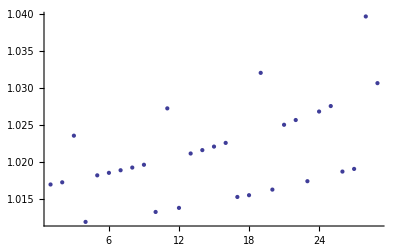

```mathematica
ListPlot[d]
```

```mathematica
Plot[ⅇ^(-t)/ⅇ^(-t-1), {t, 0, 5}]
```

-Graphics-

```mathematica
Length[A1]
```

30

```mathematica
Length[A2]
```

30

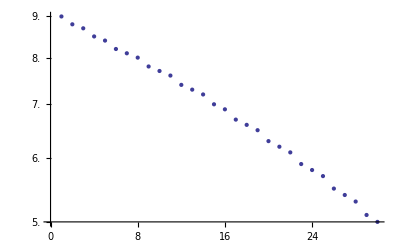

```mathematica
ListLogPlot[A1]
```

Frequenz = 20 s für 10 Perioden

gemessen durch Simon

## mit Dämpfung 0.45 A

```mathematica
A3 = {9,7.1,5.7,4.5,3.5,2.7,2.2,1.7,1.4,1};
```

```mathematica
A4 = {9,7.2,5.8,4.5,3.5,2.7,2.1,1.6,1.2,0.9};
```

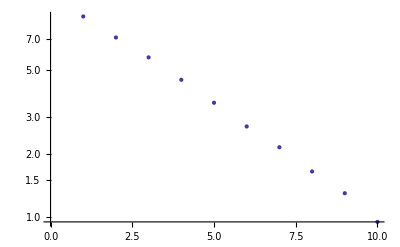

```mathematica
ListLogPlot[Table[(A3[[i]]+A4[[i]])/2, {i, 1, Length[A3]}]]
```

```mathematica
Length[A3]
```

10

```mathematica
Log[9]//N
```

2.19722

```mathematica
Length[A4]
```

10

```mathematica
d = Table[(A3[[i]]+A4[[i]])/(A3[[i+1]]+A4[[i+1]]), {i, 1, Length[A3]-1}]
```

{1.25874,1.24348,1.27778,1.28571,1.2963,1.25581,1.30303,1.26923,1.36842}

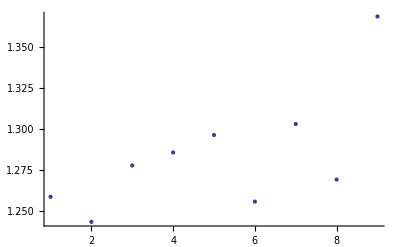

```mathematica
ListPlot[d]
```

Frequenz 20 = s für 10 Periode
A3 gemessen durch batritschia
A4 gemessen durch Simon

## mit Dämpfung 0.6 A

```mathematica
A5 = {9,6,4,2.6,1.7,1.1,0.6,0.4,0.2,0.1};
A6 = {9,6,4,2.7,1.8,1.2,0.7,0.4,0.3,0.1};
```

```mathematica
Length[A5] == Length[A6]
```

True

```mathematica
d = Table[(A5[[i]]+A6[[i]])/(A5[[i+1]]+A6[[i+1]]), {i, 1, Length[A3]-1}]
```

{3/2,3/2,1.50943,1.51429,1.52174,1.76923,1.625,1.6,2.5}

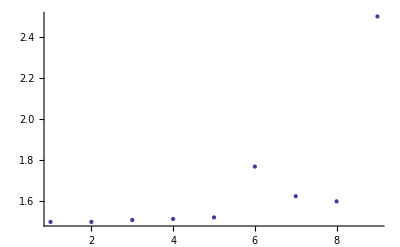

```mathematica
ListPlot[d]
```

```mathematica
f6 = 1/(20/10);
```

Periode = 20 s für 10 Perioden

patritschia liest werte ab und simon misst die zeit;

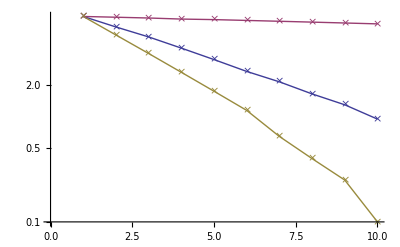

```mathematica
ListLogPlot[{
Table[(A3[[i]] + A4[[i]])/2, {i, 1, Length[A3]}], Table[(A1[[i]]+A2[[i]])/2, {i, 1, Length[A3]}], Table[(A5[[i]]+A6[[i]])/2, {i, 1, Length[A3]}]}, 
Joined->True, 
PlotMarkers->{{"×", Medium}}]
```

```mathematica
1/(Log[A1[[Length[A1]]]]-Log[A1[[1]]])//N
```

-1.7013

```mathematica
1/(Log[A3[[Length[A3]]]]-Log[A3[[1]]])//N
```

-0.45512

```mathematica
1/(Log[A5[[Length[A5]]]]-Log[A5[[1]]])//N
```

-0.222232

## Aufgabe 2

## mit 0.6 A

```mathematica
A7 = Table[(A5[[i]] + A6[[i]])/2, {i, 1, 10}];
```

resonanzfreq

```mathematica
alpha6 = -f6*Log[A7[[10]]/A7[[1]]]/9
```

0.249989

```mathematica
omega6 = Sqrt[(2π*f6)^2-2alpha6^2] / 2/π
```

0.496824

```mathematica
1/omega6
```

2.01279

```mathematica
A8 = {{22, 1.3},{20,2.1},{18,1.05},{16,0.45},{21,1.9},{21.5,1.7},{19,1.4},{20.5,2.15}};
```

```mathematica
A25 = Table[{10/(A8[[i]][[1]]), A8[[i]][[2]]}, {i, 1, Length[A8]}]
```

{{5/11,1.3},{1/2,2.1},{5/9,1.05},{5/8,0.45},{10/21,1.9},{0.465116,1.7},{10/19,1.4},{0.487805,2.15}}

```mathematica
9/Sqrt[2]//N
```

6.36396

```mathematica
m = 2.15*alpha0
```

0.019412

```mathematica
Feps[o_] = m/Sqrt[(o-omega0)^2+alpha0^2]
```

0.019412/(√(0.0000815198+(-0.499996+o)^2))

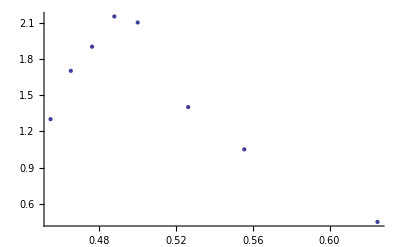

```mathematica
a=ListPlot[A25]
```

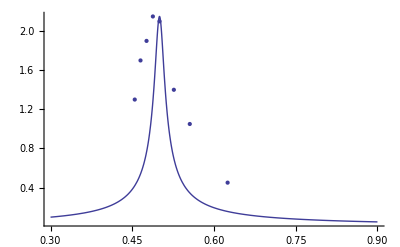

```mathematica
Show[{a, Plot[Feps[o], {o, 0.3, 0.9}, PlotRange->{0, 10}]}]
```

## mit 0.45 A

```mathematica
A9 = Table[(A3[[i]] + A4[[i]])/2, {i, 1, 10}];
```

```mathematica
alpha45 = -f6*Log[A9[[10]]/A9[[1]]]/9
```

0.124918

```mathematica
omega45 = Sqrt[(2π*f6)^2-2alpha45^2] / 2/π
```

0.499209

```mathematica
1/omega45
```

2.00317

```mathematica
A10 = {{20.5, 3.45},{19,1.5},{19.5,2.9},{20,3.55},{20.2,3.6},{18.2,1.25},{19.1,2.5}};
```

```mathematica
3.6/Sqrt[2]
```

2.54558

```mathematica
A24 = Table[{10/(A10[[i]][[1]]), A10[[i]][[2]]}, {i, 1, Length[A10]}]
```

{{0.487805,3.45},{10/19,1.5},{0.512821,2.9},{1/2,3.55},{0.49505,3.6},{0.549451,1.25},{0.52356,2.5}}

```mathematica
m = 3.6*alpha0
```

0.0325038

```mathematica
Feps[o_] = m/Sqrt[(o-omega0)^2+alpha0^2]
```

0.0325038/(√(0.0000815198+(-0.499996+o)^2))

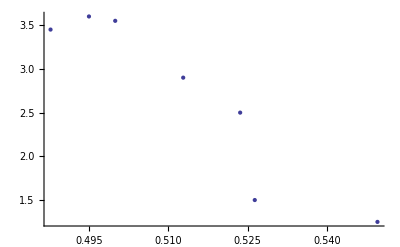

```mathematica
a = ListPlot[A24]
```

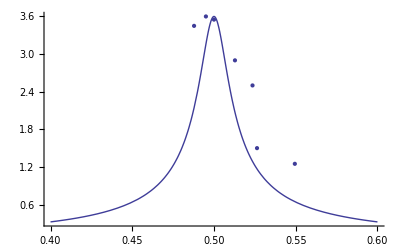

```mathematica
Show[{a, Plot[Feps[o], {o, 0.4, 0.6}, PlotRange->{0, 10}]}]
```

## ohne

```mathematica
A11 = Table[(A1[[i]] + A2[[i]])/2, {i, 1, 10}];
```

```mathematica
alpha0 = -f6*Log[A11[[10]]/A11[[1]]]/9
```

0.00902883

```mathematica
omega0 = Sqrt[(2π*f6)^2-2alpha0^2] / 2/π
```

0.499996

```mathematica
1/omega0
```

2.00002

```mathematica
A12 = {{19.1,4.1},{20,8.6},{20.5,4.3},{22.0,1.7},{21,2.9},{18.5,1.5},{19.5,6}};
```

```mathematica
3.6/Sqrt[2]
```

2.54558

```mathematica
A23 = Table[{10/(A12[[i]][[1]]), A12[[i]][[2]]}, {i, 1, Length[A12]}]
```

{{0.52356,4.1},{1/2,8.6},{0.487805,4.3},{0.454545,1.7},{10/21,2.9},{0.540541,1.5},{0.512821,6}}

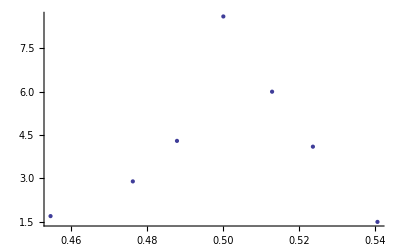

```mathematica
a = ListPlot[A23]
```

```mathematica
m = 8.6*alpha0
```

0.0776479

```mathematica
Feps[o_] = m/Sqrt[(o-omega0)^2+alpha0^2]
```

0.0776479/(√(0.0000815198+(-0.499996+o)^2))

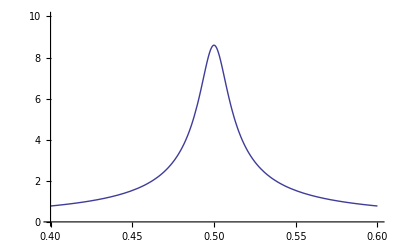

```mathematica
b = Plot[Feps[o], {o, 0.4, 0.6}, PlotRange->{0, 10}]
```

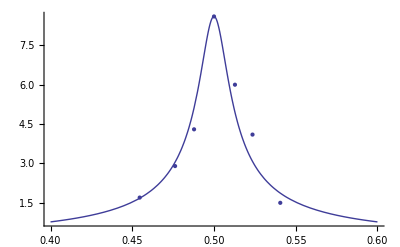

```mathematica
Show[{a, b}]
```